## QCD Phase Transition Diagrams in comparison

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Numerical Values from the linear sigmal model*)
h0=0.0017710920000000002;(*external field from the linear sigma model*)
TTCP=0.076277777815741;(*tempereture on the tricritical point (h=0)*)
muTCP=0.27957006500321346;(*chemical potential on the tricritical point (h=0)*)
sigTCP=0;
TCEP=0.04184538618740476;(*temperature on the critical endpoint (h≠0)*)
muCEP=0.31568415962210034;(*chemical potential on the critical endpoint (h≠0)*)
sigCEP=0.05383246620021203;
```

```mathematica
linesNFP=Import["phaseTransitionLine_nfp.wdx"];
linesESB=Import["phaseTransitionLine_ESB.wdx"];
```

```mathematica
text=Show[Graphics[{Black,FontSize->18,Text["TCP",{muTCP-0.02,TTCP}]}],Graphics[{Black,FontSize->18,Text["CEP",{muCEP+0.02,TCEP}]}],Graphics[{Black,FontSize->18,Text["crossover",{muTCP-0.1,TTCP+0.09}]}],Graphics[{Black,FontSize->18,Text["2nd",{muTCP-0.15,TTCP+0.06}]}],Graphics[{Black,FontSize->18,Text["1st",{muTCP+0.015,TTCP-0.035}]}]];
```

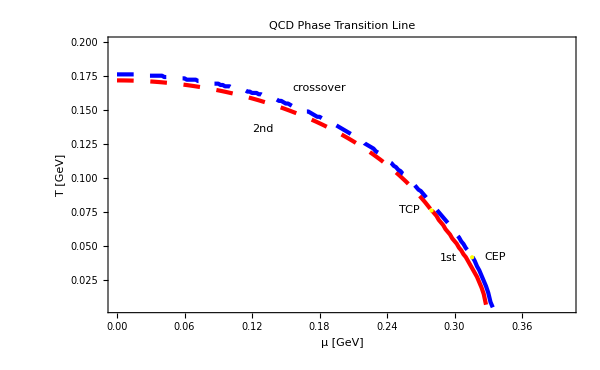

```mathematica
Show[linesNFP,linesESB,text]
```